```mathematica
Clear["Global`*"]
```

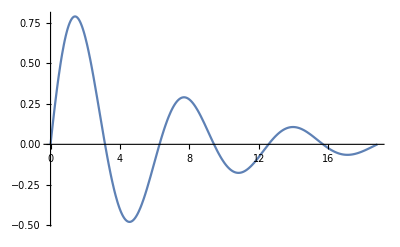

```mathematica
f[x_]:=Exp[(-Abs[x])/(2π)]Sin[x]
Plot[f[x],{x,0,6π}]
exactValue=Integrate[f[x],{x,0,6π}]
```

```mathematica
simpsonCoefficients={1/3,4/3,2/3}
trapezCoefficients={1/2,1}
Simpson[f_,a_,b_,n_]:=(b-a)/n(f[a]simpsonCoefficients[[1]]+
Sum[N[f[a+i(b-a)/n]]simpsonCoefficients[[ 2+Mod[i+1,2] ]],{i,1,n-1}]
+f[b] simpsonCoefficients[[1]])/.n->n+Mod[n,2]
Trapez[f_,a_,b_,n_]:=(b-a)/n(f[a]trapezCoefficients[[1]]+
Sum[N[f[a+i(b-a)/n]]trapezCoefficients[[ 2+Mod[i+1,1] ]],{i,1,n-1}]
+f[b] trapezCoefficients[[1]])/.n->n+Mod[n,2]
```

```mathematica
trapezDeviations={#,Abs[Trapez[f,0,6π,#]-exactValue]}&/@Range[100,1000,100];
simpsonDeviations={#,Abs[Simpson[f,0,6π,#]-exactValue]}&/@Range[100,1000,100];
```

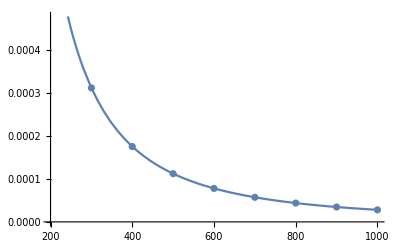

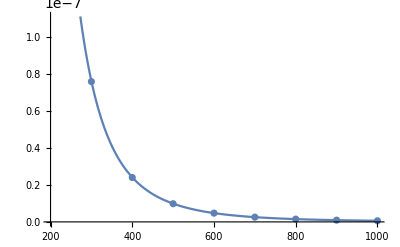

```mathematica
fitAndPlot[data_,exponent_]:=
Show[Plot[NonlinearModelFit[data,b(x)^-exponent,{b},x][y],{y,200,1000}],ListPlot[data]]
fitAndPlot[trapezDeviations,2]
fitAndPlot[simpsonDeviations/.{n_,d_}:>{n,d},4]
```